```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_fixed_nu/";
```

```mathematica
If[DirectoryQ[outputdir],DeleteDirectory[outputdir,DeleteContents->True];Print["Directory deleted"],Print["Directory does not exist"]]
```

Directory deleted

{{:0,:1,:2},{1.,0,0},{0.9,0,0},{0.8,0,0},{0.7,0,0},{0.6,0,0},{0.5,0,0},{0.4,0,0},{0.3,0,0},{0.2,0,0},{0.1,0,0},{0.,0,0}}

{{1.,0,0},{0.9,0,0},{0.8,0,0},{0.7,0,0},{0.6,0,0},{0.5,0,0},{0.4,0,0},{0.3,0,0},{0.2,0,0},{0.1,0,0},{0.,0,0}}

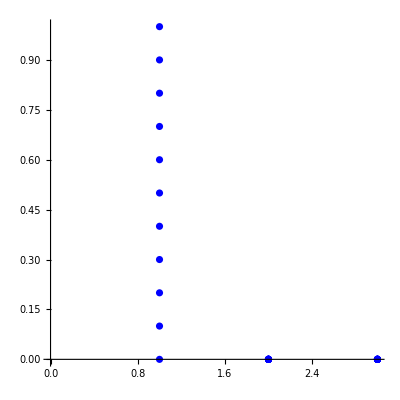

11

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.5,1.,0,0},{2.71621,0.9,0,0},{1.98906,0.8,0,0},{0.542066,0.7,0,0},{-0.462186,0.6,0,0},{-0.21537,0.5,0,0},{1.37,0.4,0,0},{2.68383,0.3,0,0},{2.1872,0.2,0,0},{0.218591,0.1,0,0},{-0.5,0.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_fixed_nu/psi.csv

```mathematica
(*write H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{1.32212,1.,0,0},{-0.469889,0.9,0,0},{-2.23686,0.8,0,0},{-2.54863,0.7,0,0},{-0.719864,0.6,0,0},{1.50029,0.5,0,0},{2.7108,0.4,0,0},{0.671121,0.3,0,0},{-1.95868,0.2,0,0},{-2.2314,0.1,0,0},{0.5,0.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_fixed_nu/mu.csv

```mathematica
(*write u from ODE to csv file*)
```

```mathematica
tabu=Table[Flatten[{{X1[x]-Xr[x][[1]],X2[x]-Xr[x][[2]],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabu,{"f:0","f:1","f:2",":0",":1",":2"}]
```

{{f:0,f:1,f:2,:0,:1,:2},{-0.547431,-1.16121,0,1.,0,0},{-0.220823,-1.04957,0,0.9,0,0},{0.0739064,-0.882241,0,0.8,0,0},{0.101937,-0.640646,0,0.7,0,0},{-0.0788908,-0.655693,0,0.6,0,0},{-0.25997,-0.793333,0,0.5,0,0},{-0.423258,-0.648918,0,0.4,0,0},{-0.139839,-0.373257,0,0.3,0,0},{0.279178,-0.182448,0,0.2,0,0},{0.268182,0.124705,0,0.1,0,0},{-9.60566×10^-22,-3.82441×10^-22,0,0.,0,0}}

```mathematica
Export[outputdir<>"u.csv",tabu]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode_fixed_nu/u.csv